-Graphics-

# Wikidata

## Easy Access to the knowledge base

…that anyone can edit.

## Outline

### Intro

From Wikipedia to Wikidata

### Basics

Search and Data Access

External Identifiers

Relationship to Entities

### Advanced Features

Result Forms

Quantities and Units

Geographic Data

Language Option

### Expert Features

Queries

Geo Lookup

Qualifiers and References

### Behind the Scenes

SPARQL

Unit Mapping

## What Is Wikipedia?

Launched: 2001.

https://en.wikipedia.org/wiki/Caffeine

### Human-Readable Text

-Graphics-

### Language Links

### Infoboxes

-Graphics-

## Wikipedia: The Problem

Spring 2013.

### Language Links

...
-Graphics-
...

Each language version links to every other version. About 300 languages (demonstrating with 30):

```mathematica
CompleteGraph[
(*300*)30,
DirectedEdges->True
]
```

-Graphics-

### Infoboxes

#### Duplication

Information repeated across language versions.

#### Machine Access

Hard to query:
-Graphics-

## Wikidata: The Solution

Launched: Fall 2012‎.

http://www.wikidata.org/entity/Q1

### Items

Represent concepts.

### Wikipedia Links

Each item links to Wikipedia:

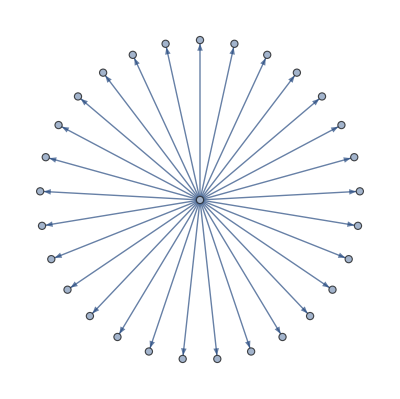

```mathematica
StarGraph[
(*300*)30,
DirectedEdges->True
]
```

### Properties

Link items to other items or values.

## Wikidata: Statistics

April 2020.

### Items

83 million.

### Properties

8 thousand.

### Edits

> 1 billion.

### Active Editors

25 thousand.
(active: at least 1 edit in the last 30 days)

## Examples

### Items

Q1: Universe
Q2: Earth
...
Q5: human
...
Q199: 1 (the number one)
...
Q506: flower
...
Q102231: rose
...
Q5070208: kangaroo

### Properties

...
P18: image
...
P31: instance of
...
P279: subclass of
...
P625: coordinates
...
P2044: elevation
P2045: orbital inclination
P2046: area
P2047: duration
P2048: height
P2049: width
...
P6670: musical quotation or excerpt
...

## Basics

Search and Data Access

External Identifiers

Relationship to Entities

## Search and Data Access

### Search

Search for an item:

```mathematica
WikidataSearch["elephant"]
```

{ExternalIdentifier[WikidataID,Q7378,<|Label→elephant,Description→trunk-bearing large mammal|>]Wikidataelephanthttp://www.wikidata.org/entity/Q7378,ExternalIdentifier[WikidataID,Q1163943,<|Label→Elephant,Description→2003 drama film directed by Gus Van Sant|>]WikidataElephanthttp://www.wikidata.org/entity/Q1163943,ExternalIdentifier[WikidataID,Q580496,<|Label→Elephant,Description→Rock album|>]WikidataElephanthttp://www.wikidata.org/entity/Q580496,ExternalIdentifier[WikidataID,Q246531,<|Label→Elephant,Description→Wikimedia disambiguation page|>]WikidataElephanthttp://www.wikidata.org/entity/Q246531,ExternalIdentifier[WikidataID,Q888626,<|Label→Pe-Hor,Description→provisional name of the first known predynastic Egypt ruler (existence disputed)|>]WikidataPe-Horhttp://www.wikidata.org/entity/Q888626,ExternalIdentifier[WikidataID,Q1247466,<|Label→Alfil,Description→fairy chess piece; jumps two squares diagonally|>]WikidataAlfilhttp://www.wikidata.org/entity/Q1247466,ExternalIdentifier[WikidataID,Q647433,<|Label→Amazon,Description→fairy chess piece that can move like a queen or a knight|>]WikidataAmazonhttp://www.wikidata.org/entity/Q647433,ExternalIdentifier[WikidataID,Q400018,<|Label→Elephant,Description→1989 film directed by Alan John Clarke|>]WikidataElephanthttp://www.wikidata.org/entity/Q400018,ExternalIdentifier[WikidataID,Q7882643,<|Label→Elephant,Description→single|>]WikidataElephanthttp://www.wikidata.org/entity/Q7882643,ExternalIdentifier[WikidataID,Q20200987,<|Label→Elephant,Description→fresco from Hermitage of San Baudelio. Casillas de Berlanga (Soria)|>]WikidataElephanthttp://www.wikidata.org/entity/Q20200987}

Search a property:

```mathematica
WikidataSearch["Property"->"height"]
```

{ExternalIdentifier[WikidataID,P2044,<|Label→elevation above sea level,Description→height of the item (geographical object) as measured relative to sea level|>]Wikidataelevation above sea levelhttp://www.wikidata.org/entity/P2044,ExternalIdentifier[WikidataID,P2048,<|Label→height,Description→vertical length of an entity|>]Wikidataheighthttp://www.wikidata.org/entity/P2048,ExternalIdentifier[WikidataID,P2793,<|Label→clearance,Description→distance between surface under bridge and bottom of a bridge deck|>]Wikidataclearancehttp://www.wikidata.org/entity/P2793,ExternalIdentifier[WikidataID,P2923,<|Label→focal height,Description→height of the lamp of a lighthouse from water level|>]Wikidatafocal heighthttp://www.wikidata.org/entity/P2923}

### Data

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant","Description"->"trunk-bearing large mammal"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378,ExternalIdentifier["WikidataID","P2048",<|"Label"->"height","Description"->"vertical length of an entity"|>]"Wikidata""height"http://www.wikidata.org/entity/P2048]
```

{4. m}

## External Identifiers

An “entity” in an external identifier system:

```mathematica
ExternalIdentifier["WikidataID","Q7378"]
```

ExternalIdentifier[WikidataID,Q7378]WikidataQ7378http://www.wikidata.org/entity/Q7378

Include a human-readable label:

```mathematica
ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant"|>]
```

ExternalIdentifier[WikidataID,Q7378,<|Label→elephant|>]Wikidataelephanthttp://www.wikidata.org/entity/Q7378

## External Identifiers

### Content

Access basic information:

```mathematica
ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378["Type"]
```

WikidataID

```mathematica
ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378["ExternalID"]
```

Q7378

```mathematica
ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378["Label"]
```

elephant

### Derived Information

Some types support the "URL" property:

```mathematica
ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378["URL"]
```

URL[http://www.wikidata.org/entity/Q7378]

## External Identifier Types

### Examples

```mathematica
ExternalIdentifier["DOI","10.3847/2041-8213/ab0ec7"]
```

ExternalIdentifier[DOI,10.3847/2041-8213/ab0ec7]DOI10.3847/2041-8213/ab0ec7https://doi.org/10.3847/2041-8213/ab0ec7

```mathematica
ExternalIdentifier["ISBN10","978-84-339-1247-3"]
```

ExternalIdentifier[ISBN10,978-84-339-1247-3]ISBN-10978-84-339-1247-3urn:ISBN:978-84-339-1247-3

```mathematica
ExternalIdentifier["InChIKey","RYYVLZVUVIJVGH-UHFFFAOYSA-N"]
```

ExternalIdentifier[InChIKey,RYYVLZVUVIJVGH-UHFFFAOYSA-N]InChIKeyRYYVLZVUVIJVGH-UHFFFAOYSA-N

### All Types

```mathematica
$ExternalIdentifierTypes
```

## Wikidata Input Types

Not just “WikidataID”.

### Any Identifier Type

Look up data by ISBN:

```mathematica
WikidataData[ExternalIdentifier["ISBN10","978-84-339-1247-3"]"ISBN-10""978-84-339-1247-3"urn:ISBN:978-84-339-1247-3,{ExternalIdentifier["WikidataID","P1476",<|"Label"->"title","Description"->"published title of a work, such as a newspaper article, a literary work, a website, or a performance work"|>]"Wikidata""title"http://www.wikidata.org/entity/P1476,ExternalIdentifier["WikidataID","P50",<|"Label"->"author","Description"->"main creator(s) of a written work (use on works, not humans); use P2093 when Wikidata item is unknown or does not exist"|>]"Wikidata""author"http://www.wikidata.org/entity/P50,ExternalIdentifier["WikidataID","P577",<|"Label"->"publication date","Description"->"date or point in time when a work was first published or released"|>]"Wikidata""publication date"http://www.wikidata.org/entity/P577},"Dataset"]
```

### Entities

Use an entity as input:

```mathematica
WikidataData[Entity["Person","DouglasAdams::gh8qf"],"Dataset"]
```

## Relationship to Entities

From entity to Wikidata item:

```mathematica
WikidataData[Entity["Person","DouglasAdams::gh8qf"],"WikidataID"]
```

{ExternalIdentifier[WikidataID,Q42,<|Label→Douglas Adams,Description→English writer and humorist|>]WikidataDouglas Adamshttp://www.wikidata.org/entity/Q42}

And back:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q42",<|"Label"->"Douglas Adams","Description"->"English writer and humorist"|>]"Wikidata""Douglas Adams"http://www.wikidata.org/entity/Q42,"Entity"]
```

{Douglas Adams}

### Any ID

Go from any ID type to any other ID type:

```mathematica
WikidataData[ExternalIdentifier["ISNI","0000 0001 0871 1294"]"ISNI""0000 0001 0871 1294"http://www.isni.org/0000 0001 0871 1294,{"Entity","WikidataID",ExternalIdentifier["WikidataID","P227",<|"Label"->"GND ID","Description"->"identifier from an international authority file of names, subjects, and organizations (please don't use type n = name, disambiguation) - Deutsche Nationalbibliothek"|>]"Wikidata""GND ID"http://www.wikidata.org/entity/P227,ExternalIdentifier["WikidataID","P268",<|"Label"->"Bibliothèque nationale de France ID","Description"->"identifier for the subject issued by BNF (Bibliothèque nationale de France). Format: 8 digits followed by a check-digit or letter, do not include the initial 'cb'."|>]"Wikidata""Bibliothèque nationale de France ID"http://www.wikidata.org/entity/P268}]
```

{{Angela Merkel},{ExternalIdentifier[WikidataID,Q567,<|Label→Angela Merkel,Description→Chancellor of Germany|>]WikidataAngela Merkelhttp://www.wikidata.org/entity/Q567},{ExternalIdentifier[GNDID,119545373]GND119545373http://d-nb.info/gnd/119545373},{ExternalIdentifier[ExternalIdentifier[WikidataID,P268,<|Label→Bibliothèque nationale de France ID,Description→identifier for the subject issued by BNF (Bibliothèque nationale de France). Format: 8 digits followed by a check-digit or letter, do not include the initial 'cb'.|>]WikidataBibliothèque nationale de France IDhttp://www.wikidata.org/entity/P268,15023978d]Wikidata Bibliothèque nationale de France ID15023978d}}

## Advanced Features

Result Forms

Quantities and Units

Geographic Data

Language Option

## Result Forms

How to “decorate” the result.

### List of Items

The default result is a list with one element per input item:

```mathematica
WikidataData[{ExternalIdentifier["WikidataID","Q7391",<|"Label"->"Anthophila","Description"->"clade of insects"|>]"Wikidata""Anthophila"http://www.wikidata.org/entity/Q7391,ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant","Description"->"trunk-bearing large mammal"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378,ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089},ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487]
```

{{🐝},{🐘},{🦒}}

#### Association

```mathematica
WikidataData[{ExternalIdentifier["WikidataID","Q7391",<|"Label"->"Anthophila","Description"->"clade of insects"|>]"Wikidata""Anthophila"http://www.wikidata.org/entity/Q7391,ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant","Description"->"trunk-bearing large mammal"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378,ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089},ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487,"Association"]
```

<|ExternalIdentifier[WikidataID,Q7391,<|Label→Anthophila,Description→clade of insects|>]WikidataAnthophilahttp://www.wikidata.org/entity/Q7391→{🐝},ExternalIdentifier[WikidataID,Q7378,<|Label→elephant,Description→trunk-bearing large mammal|>]Wikidataelephanthttp://www.wikidata.org/entity/Q7378→{🐘},ExternalIdentifier[WikidataID,Q862089,<|Label→giraffe,Description→genus of mammals|>]Wikidatagiraffehttp://www.wikidata.org/entity/Q862089→{🦒}|>

#### Dataset

```mathematica
WikidataData[{ExternalIdentifier["WikidataID","Q7391",<|"Label"->"Anthophila","Description"->"clade of insects"|>]"Wikidata""Anthophila"http://www.wikidata.org/entity/Q7391,ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant","Description"->"trunk-bearing large mammal"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378,ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089},ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487,"Dataset"]
```

## Result Forms

### List of Properties

The default result is a list with one element per input property:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089,{ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487,ExternalIdentifier["WikidataID","P171",<|"Label"->"parent taxon","Description"->"closest parent taxon of the taxon in question"|>]"Wikidata""parent taxon"http://www.wikidata.org/entity/P171}]
```

{{🦒},{ExternalIdentifier[WikidataID,Q186154,<|Label→Giraffidae,Description→family of mammals|>]WikidataGiraffidaehttp://www.wikidata.org/entity/Q186154}}

#### Association

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089,{ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487,ExternalIdentifier["WikidataID","P171",<|"Label"->"parent taxon","Description"->"closest parent taxon of the taxon in question"|>]"Wikidata""parent taxon"http://www.wikidata.org/entity/P171},"Association"]
```

<|ExternalIdentifier[WikidataID,P487,<|Label→Unicode character,Description→Unicode character representing the item|>]WikidataUnicode characterhttp://www.wikidata.org/entity/P487→{🦒},ExternalIdentifier[WikidataID,P171,<|Label→parent taxon,Description→closest parent taxon of the taxon in question|>]Wikidataparent taxonhttp://www.wikidata.org/entity/P171→{ExternalIdentifier[WikidataID,Q186154,<|Label→Giraffidae,Description→family of mammals|>]WikidataGiraffidaehttp://www.wikidata.org/entity/Q186154}|>

### All Lists

Form the outer product of values:

```mathematica
WikidataData[
{ExternalIdentifier["WikidataID","Q7391",<|"Label"->"Anthophila","Description"->"clade of insects"|>]"Wikidata""Anthophila"http://www.wikidata.org/entity/Q7391,ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant","Description"->"trunk-bearing large mammal"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378,ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089},
{ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487,ExternalIdentifier["WikidataID","P171",<|"Label"->"parent taxon","Description"->"closest parent taxon of the taxon in question"|>]"Wikidata""parent taxon"http://www.wikidata.org/entity/P171}
]
```

{{{🐝},{ExternalIdentifier[WikidataID,Q324132,<|Label→Apoidea,Description→superfamily of insects|>]WikidataApoideahttp://www.wikidata.org/entity/Q324132}},{{🐘},{}},{{🦒},{ExternalIdentifier[WikidataID,Q186154,<|Label→Giraffidae,Description→family of mammals|>]WikidataGiraffidaehttp://www.wikidata.org/entity/Q186154}}}

#### Dataset

```mathematica
WikidataData[
{ExternalIdentifier["WikidataID","Q7391",<|"Label"->"Anthophila","Description"->"clade of insects"|>]"Wikidata""Anthophila"http://www.wikidata.org/entity/Q7391,ExternalIdentifier["WikidataID","Q7378",<|"Label"->"elephant","Description"->"trunk-bearing large mammal"|>]"Wikidata""elephant"http://www.wikidata.org/entity/Q7378,ExternalIdentifier["WikidataID","Q862089",<|"Label"->"giraffe","Description"->"genus of mammals"|>]"Wikidata""giraffe"http://www.wikidata.org/entity/Q862089},
{ExternalIdentifier["WikidataID","P487",<|"Label"->"Unicode character","Description"->"Unicode character representing the item"|>]"Wikidata""Unicode character"http://www.wikidata.org/entity/P487,ExternalIdentifier["WikidataID","P171",<|"Label"->"parent taxon","Description"->"closest parent taxon of the taxon in question"|>]"Wikidata""parent taxon"http://www.wikidata.org/entity/P171},
"Dataset"
]
```

## Quantities and Units

Request the mass of various items:

```mathematica
WikidataData[{ExternalIdentifier["WikidataID","Q544",<|"Label"->"Solar System","Description"->"planetary system of the Sun"|>]"Wikidata""Solar System"http://www.wikidata.org/entity/Q544,ExternalIdentifier["WikidataID","Q556",<|"Label"->"hydrogen","Description"->"chemical element with symbol H and atomic number 1; lightest and most abundant chemical substance in the universe"|>]"Wikidata""hydrogen"http://www.wikidata.org/entity/Q556,ExternalIdentifier["WikidataID","Q2",<|"Label"->"Earth","Description"->"third planet from the Sun in the Solar System"|>]"Wikidata""Earth"http://www.wikidata.org/entity/Q2,ExternalIdentifier["WikidataID","Q76",<|"Label"->"Barack Obama","Description"->"44th president of the United States"|>]"Wikidata""Barack Obama"http://www.wikidata.org/entity/Q76},ExternalIdentifier["WikidataID","P2067",<|"Label"->"mass","Description"->"mass (in colloquial usage also known as weight) of the item"|>]"Wikidata""mass"http://www.wikidata.org/entity/P2067,"Association"][[All,1]]
```

<|ExternalIdentifier[WikidataID,Q544,<|Label→Solar System,Description→planetary system of the Sun|>]WikidataSolar Systemhttp://www.wikidata.org/entity/Q544→1.0014 M_☉,ExternalIdentifier[WikidataID,Q556,<|Label→hydrogen,Description→chemical element with symbol H and atomic number 1; lightest and most abundant chemical substance in the universe|>]Wikidatahydrogenhttp://www.wikidata.org/entity/Q556→1.008 u,ExternalIdentifier[WikidataID,Q2,<|Label→Earth,Description→third planet from the Sun in the Solar System|>]WikidataEarthhttp://www.wikidata.org/entity/Q2→5972.37 Yg,ExternalIdentifier[WikidataID,Q76,<|Label→Barack Obama,Description→44th president of the United States|>]WikidataBarack Obamahttp://www.wikidata.org/entity/Q76→80. kg|>

Thanks to units, values can be sorted by mass (instead of just by numerical magnitude):

```mathematica
Sort[%]
```

<|ExternalIdentifier[WikidataID,Q556,<|Label→hydrogen,Description→chemical element with symbol H and atomic number 1; lightest and most abundant chemical substance in the universe|>]Wikidatahydrogenhttp://www.wikidata.org/entity/Q556→1.008 u,ExternalIdentifier[WikidataID,Q76,<|Label→Barack Obama,Description→44th president of the United States|>]WikidataBarack Obamahttp://www.wikidata.org/entity/Q76→80. kg,ExternalIdentifier[WikidataID,Q2,<|Label→Earth,Description→third planet from the Sun in the Solar System|>]WikidataEarthhttp://www.wikidata.org/entity/Q2→5972.37 Yg,ExternalIdentifier[WikidataID,Q544,<|Label→Solar System,Description→planetary system of the Sun|>]WikidataSolar Systemhttp://www.wikidata.org/entity/Q544→1.0014 M_☉|>

Make a diagram:

```mathematica
ListLogPlot[%]
```

-Graphics-

## Geographic Data

Retrieve the position of an item:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q243",<|"Label"->"Eiffel Tower","Description"->"tower located on the Champ de Mars in Paris, France"|>]"Wikidata""Eiffel Tower"http://www.wikidata.org/entity/Q243,"Position"]
```

{GeoPosition[{48.8583,2.29448}]}

Make a map:

```mathematica
GeoGraphics[GeoMarker[%]]
```

-Graphics-

## Geographic Data

Do not just look on Earth.

Find the position of a crater on Mars:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q3298524",<|"Label"->"Korolev","Description"->"crater on Mars"|>]"Wikidata""Korolev"http://www.wikidata.org/entity/Q3298524,"Position"]
```

{GeoPosition[{72.77,164.58},Mars]}

Make a map:

```mathematica
GeoGraphics[GeoMarker[%]]
```

-Graphics-

## Language Option

Retrieve the label of an item in Spanish:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q1",<|"Label"->"universe","Description"->"totality consisting of space, time, matter and energy"|>]"Wikidata""universe"http://www.wikidata.org/entity/Q1,"Label",Language->Entity["Language","Spanish::77gfp"]]
```

{Universo}

All language-dependent aspects respect the language choice:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q1367",<|"Label"->"monkey","Description"->"animal of the \"higher primates\" (the simians)"|>]"Wikidata""monkey"http://www.wikidata.org/entity/Q1367,"NonIdentifierProperties","Dataset",Language->Entity["Language","German::8jz29"]]
```

## Language Option

Search items by French label:

```mathematica
WikidataSearch["coeur",Language->Entity["Language","French::367gk"],MaxItems->3]
```

{ExternalIdentifier[WikidataID,Q1072,<|Label→cœur,Description→organe creux et musculaire qui assure la circulation du sang|>]Wikidatacœurhttp://www.wikidata.org/entity/Q1072,ExternalIdentifier[WikidataID,Q826930,<|Label→cœur,Description→symbole représentant un cœur|>]Wikidatacœurhttp://www.wikidata.org/entity/Q826930,ExternalIdentifier[WikidataID,Q20669022,<|Label→Tombaugh Regio,Description→regio sur Pluton|>]WikidataTombaugh Regiohttp://www.wikidata.org/entity/Q20669022}

The meaning does not depend on the embedded labels:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q1072",<|"Label"->"cœur","Description"->"organe creux et musculaire qui assure la circulation du sang"|>]"Wikidata""cœur"http://www.wikidata.org/entity/Q1072,"Classes"]
```

{ExternalIdentifier[WikidataID,Q4936952,<|Label→anatomical structure,Description→entity with a single connected inherent 3D shape that's created by coordinated expression of the organism's own DNA|>]Wikidataanatomical structurehttp://www.wikidata.org/entity/Q4936952}

Update embedded metadata:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q1072",<|"Label"->"cœur","Description"->"organe creux et musculaire qui assure la circulation du sang"|>]"Wikidata""cœur"http://www.wikidata.org/entity/Q1072,Language->Entity["Language","Italian::39fbj"]]
```

ExternalIdentifier[WikidataID,Q1072,<|Label→cuore,Description→organo muscolare, centro motore dell'apparato circolatorio|>]Wikidatacuorehttp://www.wikidata.org/entity/Q1072

## Expert Features

Queries

Geo Lookup

Qualifiers and References

## Queries

Remember entity classes?

The thee longest rivers in Italy:

```mathematica
rivers=EntityClass["River",{EntityProperty["River","Countries"]->Entity["Country","Italy"],EntityProperty["River","Length"]->TakeLargest[3]}];
```

### WolframAlpha

Get the lengths:

```mathematica
rivers["Length","Association"]
```

<|Drava→719. km,Po→652. km,Adige→410. km|>

### Wikidata

Evaluate the same query on Wikidata:

```mathematica
WikidataData[rivers,"Length","Association"]
```

<|ExternalIdentifier[WikidataID,Q171009,<|Label→Drava,Description→river in Italy, Austria, Slovenia, Croatia and Hungary|>]WikidataDravahttp://www.wikidata.org/entity/Q171009→{720. km},ExternalIdentifier[WikidataID,Q643,<|Label→Po,Description→longest river in Italy|>]WikidataPohttp://www.wikidata.org/entity/Q643→{652. km,652. km},ExternalIdentifier[WikidataID,Q13696,<|Label→Adige,Description→river in Northern Italy|>]WikidataAdigehttp://www.wikidata.org/entity/Q13696→{410. km}|>

## Geo Lookup

Look up items inside a GeoDisk.

### The Class

A disk around the center of Madrid:

```mathematica
madrid=GeoDisk[Entity["City",{"Madrid","Madrid","Spain"}],Quantity[1, "Kilometers"]];
```

Theatres inside that disk:

```mathematica
theatres=EntityClass[ExternalIdentifier["WikidataID","Q24354",<|"Label"->"theatre","Description"->"performing arts venue"|>]"Wikidata""theatre"http://www.wikidata.org/entity/Q24354,madrid];
```

### Lookup

Retrieve the positions:

```mathematica
positions=WikidataData[theatres,"Position","Association"];
Short[positions]
```

<|ExternalIdentifier[WikidataID,Q211250,<|Label→Teatro Real,Description→opera house in Madrid, Spain|>]WikidataTeatro Realhttp://www.wikidata.org/entity/Q211250→{GeoPosition[{40.4182,-3.71037}]},«25»,ExternalIdentifier[WikidataID,Q66135427]WikidataQ66135427http://www.wikidata.org/entity/Q66135427→{GeoPosition[{40.4195,-3.7026}]}|>

### Visualization

Make a map:

```mathematica
GeoListPlot[KeyValueMap[Labeled[#2[[1]],#]&,positions]]
```

-Graphics-

## Qualifiers and References

Additional information for each value.

The unqualified value is not meaningful for some applications:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q569",<|"Label"->"beryllium","Description"->"chemical element with symbol Be and atomic number 4"|>]"Wikidata""beryllium"http://www.wikidata.org/entity/Q569,ExternalIdentifier["WikidataID","P2054",<|"Label"->"density","Description"->"density of a substance with phase of matter and temperature as qualifiers"|>]"Wikidata""density"http://www.wikidata.org/entity/P2054]
```

{1.85 g/cm^3}

Include the details:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q569",<|"Label"->"beryllium","Description"->"chemical element with symbol Be and atomic number 4"|>]"Wikidata""beryllium"http://www.wikidata.org/entity/Q569,ExternalIdentifier["WikidataID","P2054",<|"Label"->"density","Description"->"density of a substance with phase of matter and temperature as qualifiers"|>]"Wikidata""density"http://www.wikidata.org/entity/P2054,Method->"StatementFormat"->"Dataset"]
```

{}

## Behind the Scenes

SPARQL

Unit Mapping

## SPARQL

The query language of the semantic web.

The SPARQL endpoint:

```mathematica
endpoint="https://query.wikidata.org/sparql";
```

Execute a simple query—get the label of an item:

```mathematica
Needs["GraphStore`"]
```

```mathematica
SPARQLExecute[endpoint,"
select * where {
  wd:Q1 rdfs:label ?label .
  filter (lang(?label) = \"en\")
}
"]
```

{<|label→RDFString[universe,en]|>}

## Symbol SPARQL

Programmatically compose SPARQL queries.

### SPARQL Patterns

Define a pattern that filters by language:

```mathematica
langFilterPattern[var_,lang_]:=SPARQLFilter[SPARQLEvaluation["lang"][var]==lang];
```

Define a pattern that finds labels:

```mathematica
labelPattern[{var_,labelVar_},lang_]:=SPARQLOptional[{
RDFTriple[var,URL["http://www.w3.org/2000/01/rdf-schema#label"],labelVar],
langFilterPattern[labelVar,lang]
}]
```

A similar pattern for the description:

```mathematica
descPattern[{var_,labelVar_},lang_]:=SPARQLOptional[{
RDFTriple[var,URL["http://schema.org/description"],labelVar],
langFilterPattern[labelVar,lang]
}]
```

Define a pattern for “entities” (items, properties, ...):

```mathematica
entityPattern[var:SPARQLVariable[varName_String],ent_URL,lang_]:={
SPARQLValues[var,{ent}],
labelPattern[{var,SPARQLVariable[varName<>"Label"]},lang],
descPattern[{var,SPARQLVariable[varName<>"Description"]},lang]
};
```

### SPARQL Queries

Make a SELECT query:

```mathematica
entityQuery[ei_ExternalIdentifier]:=SPARQLSelect[entityPattern[SPARQLVariable["Entity"],ei["ConceptURI"],"en"]];
```

Execute the query:

```mathematica
SPARQLExecute[endpoint,entityQuery[ExternalIdentifier["WikidataID","Q2"]"Wikidata""Q2"http://www.wikidata.org/entity/Q2]]
```

{<|Entity→URL[http://www.wikidata.org/entity/Q2],EntityDescription→RDFString[third planet from the Sun in the Solar System,en],EntityLabel→RDFString[Earth,en]|>}

## Unit Mapping

Units are items.

Where does the unit come from in the following example?

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q243",<|"Label"->"Eiffel Tower","Description"->"tower located on the Champ de Mars in Paris, France"|>]"Wikidata""Eiffel Tower"http://www.wikidata.org/entity/Q243,"Mass"]
```

{10000. t}

“Metric ton” is an item in Wikidata:

```mathematica
WikidataSearch["metric ton"]
```

{ExternalIdentifier[WikidataID,Q191118,<|Label→tonne,Description→metric unit of mass equal to 1000 kg|>]Wikidatatonnehttp://www.wikidata.org/entity/Q191118}

The mapping to a Wolfram Language™ unit:

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q191118",<|"Label"->"tonne","Description"->"metric unit of mass equal to 1000 kg"|>]"Wikidata""tonne"http://www.wikidata.org/entity/Q191118,ExternalIdentifier["WikidataID","P7007",<|"Label"->"Wolfram Language unit code","Description"->"input form for a unit of measurement in the Wolfram Language"|>]"Wikidata""Wolfram Language unit code"http://www.wikidata.org/entity/P7007]
```

{ExternalIdentifier[ExternalIdentifier[WikidataID,P7007,<|Label→Wolfram Language unit code,Description→input form for a unit of measurement in the Wolfram Language|>]WikidataWolfram Language unit codehttp://www.wikidata.org/entity/P7007,"MetricTons"]Wikidata Wolfram Language unit code"MetricTons"}

## Thanks

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q12769393"]"Wikidata""Q12769393"http://www.wikidata.org/entity/Q12769393,Language->#]&/@{"en","de","fr"}
```

{ExternalIdentifier[WikidataID,Q12769393,<|Label→end,Description→termination of something|>]Wikidataendhttp://www.wikidata.org/entity/Q12769393,ExternalIdentifier[WikidataID,Q12769393,<|Label→Ende,Description→Ort, an dem etwas endet|>]WikidataEndehttp://www.wikidata.org/entity/Q12769393,ExternalIdentifier[WikidataID,Q12769393,<|Label→fin,Description→où se termine quelque chose|>]Wikidatafinhttp://www.wikidata.org/entity/Q12769393}